```mathematica
ExpressionLattice[exp_]:=Block[{allVars=DeleteDuplicates[ListofVars[exp]],sets, terms, expanded, vars, edges={}},
expanded=Expand[exp];
terms=Table[expanded[[k]],{k,Length[expanded]}];
vars=Map[DeleteDuplicates[ListofVars[#]]&,terms];
Table[If[Length[vars[[from]]]==Length[vars[[to]]]+1&&Length[Intersection[vars[[from]],vars[[to]]]]==Length[vars[[from]]]-1&&Length[vars[[to]]]<Length[vars[[from]]],
AppendTo[edges,DirectedEdge[terms[[from]],terms[[to]]]]
],{from,Length[terms]},{to,Length[terms]}];
Graph[edges,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name", ImageSize->{270,270}, VertexLabelStyle->{Bold,Red}]
]
```

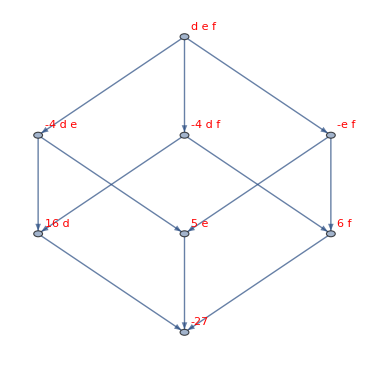

```mathematica
ExpressionLattice[ (-27+16 d+5 e-4 d e+6 f-4 d f-e f+d e f)]
```

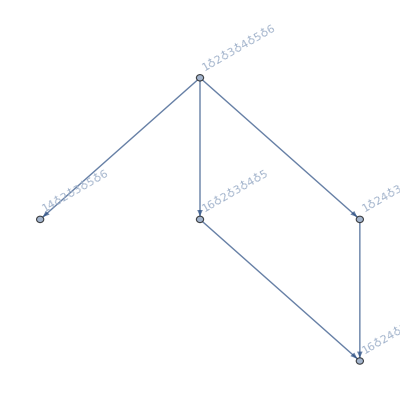

```mathematica
FormulaGraphReverse2[ FindFullFormula[ReadGrof[3]]]
```